```mathematica
k = 12;
h = 0.16;

df[x_] := -k*x
f[0.0] = 1;
f[t_] := f[t-h] + df[f[t-h]]*h

g[0.0] = 1;
g[t_] := g[t-h] / (1 + h*k)

Slider[Dynamic[k], {0, 50}]
Slider[Dynamic[h], {0.05, 1}]

Dynamic[Show[Plot[E^(-k*t), {t, 0, 1}, PlotRange->{-1, 1}], DiscretePlot[{f[t], g[t]}, {t, 0, 1, h}, Joined->True, PlotRange->{-1, 1}]]]
```

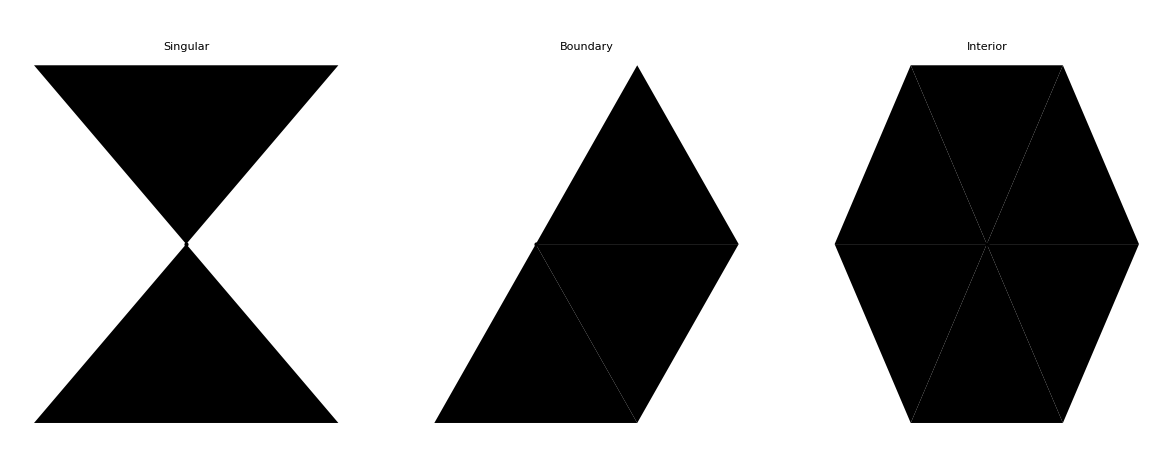

/Users/miles/Kiln/projects/fem/Figures.pdf

```mathematica
apex = {1/2, Sqrt[3]/2};
tri = {{0,0}, {1,0}, apex};
style = {FaceForm[None],EdgeForm[Blue],AbsolutePointSize[8]};

fig = GraphicsRow[{
Graphics[{Polygon[tri], Rotate[Polygon[tri], 180Degree, apex],Point[apex]},PlotLabel->"Singular", BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex], Point[apex]},PlotLabel->"Boundary",BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex],
Rotate[Polygon[tri],180Degree, apex],
Rotate[Polygon[tri],240Degree, apex],
Rotate[Polygon[tri],300Degree, apex] ,Point[apex]},PlotLabel->"Interior", BaseStyle->style]}]

Export[FileNameJoin[{NotebookDirectory[], "figures.pdf"}],fig]
```

{{0.,20.},{-20.,-20.},{-15.2695,-4.58152}}

{{0.72,0.16},{0.72,0.08},{1.2,0.16}}

{{0.48,0.08},{0.4,0.08},{0.96,0.12}}

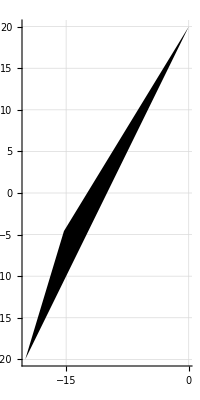

```mathematica
tri1 = {{0.000000,20.000000},{-20.000000,-20.000000},{-15.269472,-4.581519}}
tri2 = {{0.720000,0.160000},{0.720000,0.080000},{1.200000,0.160000}}
tri3 = {{0.480000,0.080000}, {0.400000,0.080000}, {0.960000,0.120000}}
Graphics[{Polygon[tri1]},Axes->True, GridLines->True]
```

{{{0.65625,0.164062},{0.765625,0.164062},{0.65625,0.246094}},{{0.65625,0.246094},{0.765625,0.164062},{0.765625,0.300781}},{{1.64063,0.273438},{1.69531,0.273438},{1.66797,0.464844}},{{0.710938,1.25781},{0.710938,1.36719},{0.519531,1.36719}},{{0.710938,1.36719},{0.820312,1.42188},{0.683594,1.47656}},{{0.65625,1.58594},{0.601562,1.53125},{0.683594,1.47656}},{{0.601562,1.53125},{0.519531,1.36719},{0.683594,1.47656}},{{0.519531,1.36719},{0.710938,1.36719},{0.683594,1.47656}},{{0.820312,1.42188},{0.929688,1.47656},{0.765625,1.53125}},{{0.929688,1.47656},{0.875,1.75},{0.765625,1.53125}},{{0.875,1.75},{0.710938,1.64063},{0.765625,1.53125}},{{0.683594,1.47656},{0.820312,1.42188},{0.765625,1.53125}},{{0.710938,1.64063},{0.65625,1.58594},{0.765625,1.53125}},{{0.65625,1.58594},{0.683594,1.47656},{0.765625,1.53125}},{{0.601562,1.64063},{0.546875,1.75},{0.546875,1.69531}},{{0.546875,1.75},{0.492188,1.75},{0.546875,1.69531}},{{0.601562,1.53125},{0.601562,1.64063},{0.492188,1.61328}},{{0.382812,1.64063},{0.382812,1.58594},{0.492188,1.61328}},{{0.601562,1.64063},{0.546875,1.69531},{0.492188,1.61328}},{{0.492188,1.75},{0.382812,1.64063},{0.492188,1.61328}},{{0.546875,1.69531},{0.492188,1.75},{0.492188,1.61328}},{{0.929688,1.47656},{1.03906,1.53125},{1.03906,1.69531}},{{0.875,1.75},{0.929688,1.47656},{1.03906,1.69531}},{{1.03906,1.53125},{1.09375,1.58594},{1.03906,1.69531}},{{0.984375,1.80469},{0.875,1.75},{1.03906,1.69531}},{{1.09375,1.58594},{1.09375,1.75},{1.03906,1.69531}},{{1.09375,1.75},{0.984375,1.80469},{1.03906,1.69531}},{{1.20313,0.164062},{1.25781,0.164062},{1.25781,0.177734}},{{1.25781,0.164062},{1.3125,0.191406},{1.25781,0.177734}},{{1.14844,0.164062},{1.20313,0.164062},{1.25781,0.177734}},{{1.42188,0.21875},{1.3125,0.191406},{1.33984,0.191406}},{{1.3125,0.191406},{1.25781,0.164062},{1.33984,0.191406}},{{1.3125,0.191406},{1.42188,0.21875},{1.55859,0.4375}},{{1.42188,0.21875},{1.64063,0.273438},{1.55859,0.4375}},{{1.64063,0.273438},{1.66797,0.464844},{1.55859,0.4375}},{{1.66797,0.464844},{1.69531,0.65625},{1.55859,0.4375}},{{1.69531,0.65625},{1.69531,0.710938},{1.55859,0.4375}},{{1.25781,0.177734},{1.3125,0.191406},{1.55859,0.4375}},{{1.14844,0.164062},{1.25781,0.177734},{1.55859,0.4375}},{{0.929688,0.164062},{0.984375,0.164062},{0.875,0.232422}},{{0.984375,0.164062},{1.03906,0.164062},{0.875,0.232422}},{{1.03906,0.164062},{1.09375,0.164062},{0.875,0.232422}},{{0.765625,0.164062},{0.929688,0.164062},{0.875,0.232422}},{{0.765625,0.300781},{0.765625,0.164062},{0.875,0.232422}},{{0.65625,0.820312},{0.765625,0.300781},{0.875,0.232422}},{{1.09375,0.164062},{1.14844,0.164062},{0.875,0.232422}},{{1.14844,0.164062},{1.55859,0.4375},{0.875,0.232422}},{{1.55859,0.4375},{0.65625,0.820312},{0.875,0.232422}},{{0.65625,0.246094},{0.765625,0.300781},{0.65625,0.314453}},{{0.492188,0.21875},{0.65625,0.164062},{0.601562,0.287109}},{{0.65625,0.164062},{0.65625,0.246094},{0.601562,0.287109}},{{0.546875,0.328125},{0.492188,0.21875},{0.601562,0.287109}},{{0.65625,0.246094},{0.65625,0.314453},{0.601562,0.287109}},{{0.464844,0.492188},{0.4375,0.492188},{0.492188,0.464844}},{{0.382812,0.546875},{0.4375,0.492188},{0.423828,0.519531}},{{0.4375,0.492188},{0.464844,0.492188},{0.423828,0.519531}},{{1.85938,0.492188},{1.85938,0.546875},{1.8457,0.519531}},{{1.85938,0.546875},{1.83203,0.546875},{1.8457,0.519531}},{{1.83203,0.546875},{1.85938,0.546875},{1.83203,0.574219}},{{1.66797,0.464844},{1.69531,0.273438},{1.77734,0.382813}},{{1.83203,0.546875},{1.83203,0.574219},{1.81836,0.574219}},{{1.83203,0.574219},{1.80469,0.601562},{1.81836,0.574219}},{{1.80469,0.601562},{1.69531,0.65625},{1.73633,0.533203}},{{1.69531,0.65625},{1.66797,0.464844},{1.73633,0.533203}},{{1.8457,0.519531},{1.83203,0.546875},{1.73633,0.533203}},{{1.85938,0.492188},{1.8457,0.519531},{1.73633,0.533203}},{{1.77734,0.382813},{1.85938,0.492188},{1.73633,0.533203}},{{1.66797,0.464844},{1.77734,0.382813},{1.73633,0.533203}},{{1.81836,0.574219},{1.80469,0.601562},{1.73633,0.533203}},{{1.83203,0.546875},{1.81836,0.574219},{1.73633,0.533203}},{{0.328125,0.601562},{0.382812,0.546875},{0.355469,0.587891}},{{0.328125,0.628906},{0.328125,0.601562},{0.355469,0.587891}},{{0.382812,0.546875},{0.423828,0.519531},{0.355469,0.587891}},{{0.328125,0.601562},{0.328125,0.628906},{0.300781,0.65625}},{{1.69531,0.765625},{1.69531,0.820312},{1.66797,0.833984}},{{1.69531,0.820312},{1.64063,0.902344},{1.66797,0.833984}},{{1.69531,0.710938},{1.69531,0.765625},{1.66797,0.833984}},{{1.64063,0.902344},{1.55859,0.4375},{1.66797,0.833984}},{{1.55859,0.4375},{1.69531,0.710938},{1.66797,0.833984}},{{1.64063,0.902344},{1.69531,0.820312},{1.64063,0.929688}},{{1.58594,1.03906},{1.53125,1.09375},{1.58594,0.998047}},{{1.55859,0.4375},{1.64063,0.902344},{1.58594,0.998047}},{{1.64063,0.902344},{1.64063,0.929688},{1.58594,0.998047}},{{1.64063,0.929688},{1.58594,1.03906},{1.58594,0.998047}},{{0.820312,1.20313},{0.765625,1.20313},{0.738281,1.01172}},{{0.765625,1.20313},{0.710938,1.25781},{0.738281,1.01172}},{{1.03906,1.20313},{0.820312,1.20313},{0.738281,1.01172}},{{0.765625,0.300781},{0.65625,0.820312},{0.65625,0.369141}},{{0.65625,0.820312},{0.546875,0.4375},{0.65625,0.369141}},{{0.546875,0.4375},{0.546875,0.328125},{0.65625,0.369141}},{{0.65625,0.314453},{0.765625,0.300781},{0.65625,0.369141}},{{0.546875,0.328125},{0.601562,0.287109},{0.65625,0.369141}},{{0.601562,0.287109},{0.65625,0.314453},{0.65625,0.369141}},{{0.546875,0.4375},{0.65625,0.820312},{0.505859,0.464844}},{{0.464844,0.492188},{0.492188,0.464844},{0.505859,0.464844}},{{0.492188,0.464844},{0.546875,0.4375},{0.505859,0.464844}},{{0.273438,0.984375},{0.273438,0.710938},{0.464844,0.765625}},{{0.423828,0.519531},{0.464844,0.492188},{0.464844,0.765625}},{{0.328125,0.628906},{0.355469,0.587891},{0.464844,0.765625}},{{0.355469,0.587891},{0.423828,0.519531},{0.464844,0.765625}},{{0.273438,0.710938},{0.300781,0.65625},{0.464844,0.765625}},{{0.300781,0.65625},{0.328125,0.628906},{0.464844,0.765625}},{{0.464844,0.492188},{0.505859,0.464844},{0.464844,0.765625}},{{0.505859,0.464844},{0.65625,0.820312},{0.464844,0.765625}},{{1.53125,1.09375},{1.47656,1.14844},{1.49023,1.12109}},{{1.47656,1.14844},{1.44922,1.14844},{1.49023,1.12109}},{{1.58594,0.998047},{1.53125,1.09375},{1.49023,1.12109}},{{1.44922,1.14844},{1.47656,1.14844},{1.42188,1.17578}},{{1.36719,1.20313},{1.03906,1.20313},{1.24414,1.17578}},{{0.65625,0.820312},{1.55859,0.4375},{1.24414,1.17578}},{{1.55859,0.4375},{1.58594,0.998047},{1.24414,1.17578}},{{1.03906,1.20313},{0.738281,1.01172},{1.24414,1.17578}},{{0.738281,1.01172},{0.65625,0.820312},{1.24414,1.17578}},{{1.58594,0.998047},{1.49023,1.12109},{1.24414,1.17578}},{{1.49023,1.12109},{1.44922,1.14844},{1.24414,1.17578}},{{1.44922,1.14844},{1.42188,1.17578},{1.24414,1.17578}},{{1.42188,1.17578},{1.36719,1.20313},{1.24414,1.17578}},{{0.21875,1.25781},{0.273438,0.984375},{0.396484,1.17578}},{{0.519531,1.36719},{0.273438,1.39453},{0.396484,1.17578}},{{0.65625,0.820312},{0.738281,1.01172},{0.396484,1.17578}},{{0.710938,1.25781},{0.519531,1.36719},{0.396484,1.17578}},{{0.738281,1.01172},{0.710938,1.25781},{0.396484,1.17578}},{{0.273438,0.984375},{0.464844,0.765625},{0.396484,1.17578}},{{0.464844,0.765625},{0.65625,0.820312},{0.396484,1.17578}},{{0.519531,1.36719},{0.601562,1.53125},{0.492188,1.53125}},{{0.601562,1.53125},{0.492188,1.61328},{0.492188,1.53125}},{{0.382812,1.58594},{0.382812,1.53125},{0.492188,1.53125}},{{0.492188,1.61328},{0.382812,1.58594},{0.492188,1.53125}},{{0.382812,1.53125},{0.328125,1.47656},{0.451172,1.44922}},{{0.328125,1.47656},{0.273438,1.39453},{0.451172,1.44922}},{{0.273438,1.39453},{0.519531,1.36719},{0.451172,1.44922}},{{0.519531,1.36719},{0.492188,1.53125},{0.451172,1.44922}},{{0.492188,1.53125},{0.382812,1.53125},{0.451172,1.44922}},{{0.21875,1.36719},{0.21875,1.3125},{0.246094,1.35352}},{{0.21875,1.3125},{0.21875,1.25781},{0.246094,1.35352}},{{0.21875,1.25781},{0.396484,1.17578},{0.246094,1.35352}},{{0.396484,1.17578},{0.273438,1.39453},{0.246094,1.35352}},{{0.21875,1.42188},{0.21875,1.36719},{0.246094,1.38086}},{{0.273438,1.39453},{0.21875,1.42188},{0.246094,1.38086}},{{0.21875,1.36719},{0.246094,1.35352},{0.246094,1.38086}},{{0.246094,1.35352},{0.273438,1.39453},{0.246094,1.38086}},{{0.21875,1.42188},{0.273438,1.39453},{0.273438,1.44922}},{{0.273438,1.39453},{0.328125,1.47656},{0.273438,1.44922}}}

{0.820312,1.64063}

{{{0.765625,1.53125},{0.929688,1.47656}},{{0.875,1.75},{0.710938,1.64063}},{{0.710938,1.64063},{0.765625,1.53125}},{{0.929688,1.47656},{1.03906,1.53125}},{{1.03906,1.53125},{1.03906,1.69531}},{{1.03906,1.69531},{0.875,1.75}},{{1.36719,1.20313},{1.03906,1.20313}},{{1.03906,1.20313},{1.24414,1.17578}},{{1.24414,1.17578},{1.36719,1.20313}}}

{{1.36719,1.20313},{1.03906,1.20313},{0.820312,1.64063}}

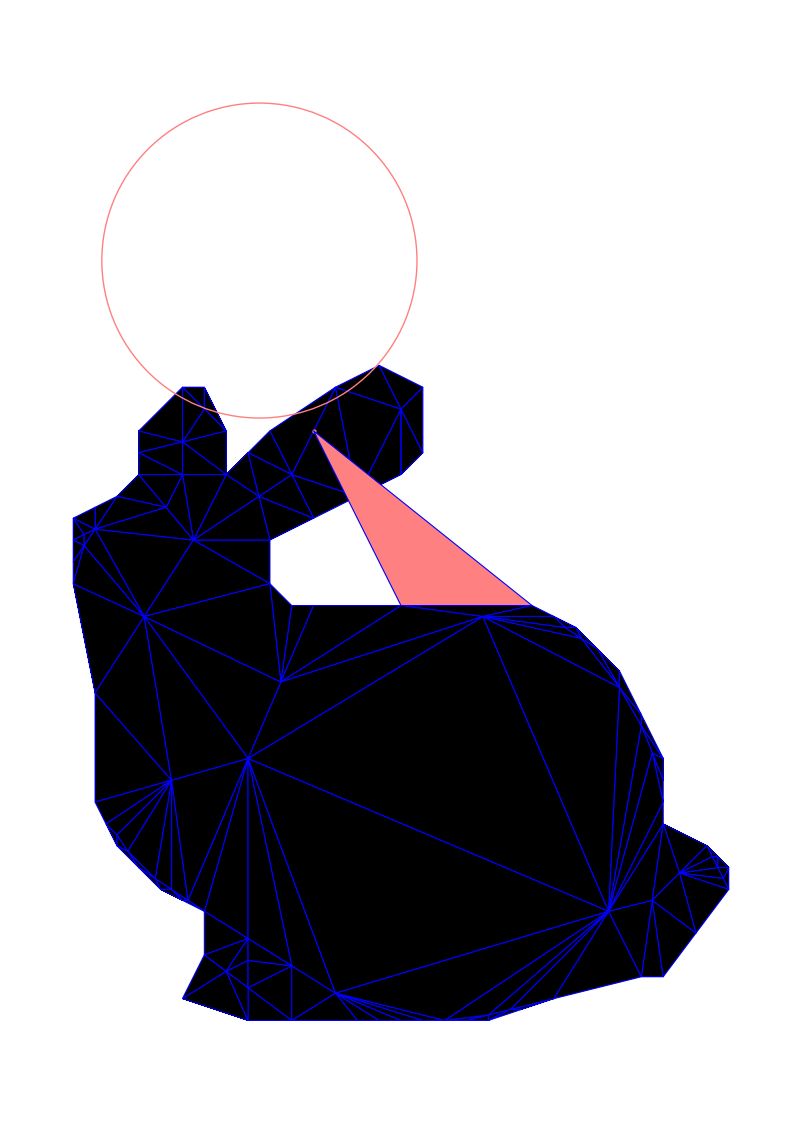

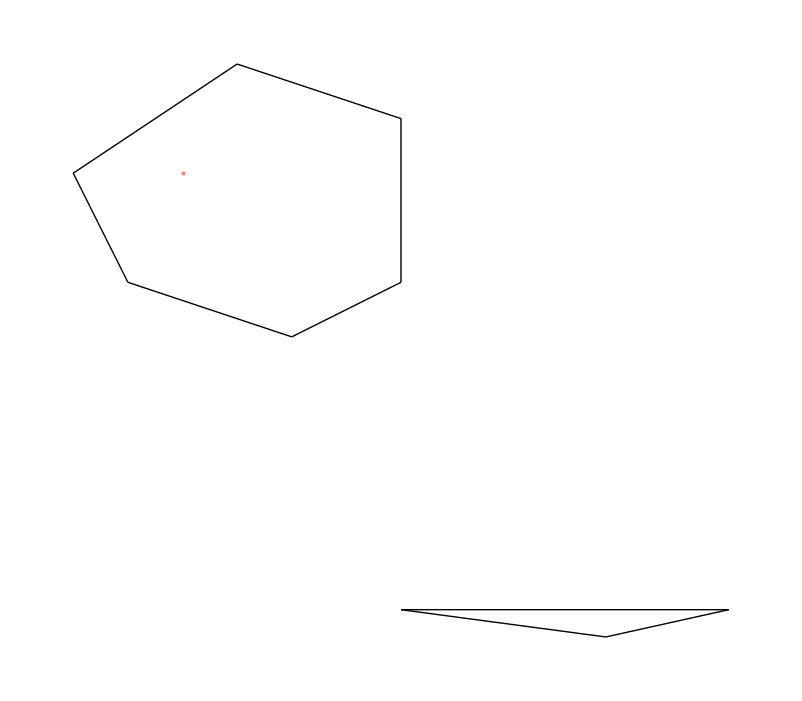

```mathematica
tris={{{0.656250,0.164062},{0.765625,0.164062},{0.656250,0.246094}},{{0.656250,0.246094},{0.765625,0.164062},{0.765625,0.300781}},{{1.640625,0.273438},{1.695312,0.273438},{1.667969,0.464844}},{{0.710938,1.257812},{0.710938,1.367188},{0.519531,1.367188}},{{0.710938,1.367188},{0.820312,1.421875},{0.683594,1.476562}},{{0.656250,1.585938},{0.601562,1.531250},{0.683594,1.476562}},{{0.601562,1.531250},{0.519531,1.367188},{0.683594,1.476562}},{{0.519531,1.367188},{0.710938,1.367188},{0.683594,1.476562}},{{0.820312,1.421875},{0.929688,1.476562},{0.765625,1.531250}},{{0.929688,1.476562},{0.875000,1.750000},{0.765625,1.531250}},{{0.875000,1.750000},{0.710938,1.640625},{0.765625,1.531250}},{{0.683594,1.476562},{0.820312,1.421875},{0.765625,1.531250}},{{0.710938,1.640625},{0.656250,1.585938},{0.765625,1.531250}},{{0.656250,1.585938},{0.683594,1.476562},{0.765625,1.531250}},{{0.601562,1.640625},{0.546875,1.750000},{0.546875,1.695312}},{{0.546875,1.750000},{0.492188,1.750000},{0.546875,1.695312}},{{0.601562,1.531250},{0.601562,1.640625},{0.492188,1.613281}},{{0.382812,1.640625},{0.382812,1.585938},{0.492188,1.613281}},{{0.601562,1.640625},{0.546875,1.695312},{0.492188,1.613281}},{{0.492188,1.750000},{0.382812,1.640625},{0.492188,1.613281}},{{0.546875,1.695312},{0.492188,1.750000},{0.492188,1.613281}},{{0.929688,1.476562},{1.039062,1.531250},{1.039062,1.695312}},{{0.875000,1.750000},{0.929688,1.476562},{1.039062,1.695312}},{{1.039062,1.531250},{1.093750,1.585938},{1.039062,1.695312}},{{0.984375,1.804688},{0.875000,1.750000},{1.039062,1.695312}},{{1.093750,1.585938},{1.093750,1.750000},{1.039062,1.695312}},{{1.093750,1.750000},{0.984375,1.804688},{1.039062,1.695312}},{{1.203125,0.164062},{1.257812,0.164062},{1.257812,0.177734}},{{1.257812,0.164062},{1.312500,0.191406},{1.257812,0.177734}},{{1.148438,0.164062},{1.203125,0.164062},{1.257812,0.177734}},{{1.421875,0.218750},{1.312500,0.191406},{1.339844,0.191406}},{{1.312500,0.191406},{1.257812,0.164062},{1.339844,0.191406}},{{1.312500,0.191406},{1.421875,0.218750},{1.558594,0.437500}},{{1.421875,0.218750},{1.640625,0.273438},{1.558594,0.437500}},{{1.640625,0.273438},{1.667969,0.464844},{1.558594,0.437500}},{{1.667969,0.464844},{1.695312,0.656250},{1.558594,0.437500}},{{1.695312,0.656250},{1.695312,0.710938},{1.558594,0.437500}},{{1.257812,0.177734},{1.312500,0.191406},{1.558594,0.437500}},{{1.148438,0.164062},{1.257812,0.177734},{1.558594,0.437500}},{{0.929688,0.164062},{0.984375,0.164062},{0.875000,0.232422}},{{0.984375,0.164062},{1.039062,0.164062},{0.875000,0.232422}},{{1.039062,0.164062},{1.093750,0.164062},{0.875000,0.232422}},{{0.765625,0.164062},{0.929688,0.164062},{0.875000,0.232422}},{{0.765625,0.300781},{0.765625,0.164062},{0.875000,0.232422}},{{0.656250,0.820312},{0.765625,0.300781},{0.875000,0.232422}},{{1.093750,0.164062},{1.148438,0.164062},{0.875000,0.232422}},{{1.148438,0.164062},{1.558594,0.437500},{0.875000,0.232422}},{{1.558594,0.437500},{0.656250,0.820312},{0.875000,0.232422}},{{0.656250,0.246094},{0.765625,0.300781},{0.656250,0.314453}},{{0.492188,0.218750},{0.656250,0.164062},{0.601562,0.287109}},{{0.656250,0.164062},{0.656250,0.246094},{0.601562,0.287109}},{{0.546875,0.328125},{0.492188,0.218750},{0.601562,0.287109}},{{0.656250,0.246094},{0.656250,0.314453},{0.601562,0.287109}},{{0.464844,0.492188},{0.437500,0.492188},{0.492188,0.464844}},{{0.382812,0.546875},{0.437500,0.492188},{0.423828,0.519531}},{{0.437500,0.492188},{0.464844,0.492188},{0.423828,0.519531}},{{1.859375,0.492188},{1.859375,0.546875},{1.845703,0.519531}},{{1.859375,0.546875},{1.832031,0.546875},{1.845703,0.519531}},{{1.832031,0.546875},{1.859375,0.546875},{1.832031,0.574219}},{{1.667969,0.464844},{1.695312,0.273438},{1.777344,0.382813}},{{1.832031,0.546875},{1.832031,0.574219},{1.818359,0.574219}},{{1.832031,0.574219},{1.804688,0.601562},{1.818359,0.574219}},{{1.804688,0.601562},{1.695312,0.656250},{1.736328,0.533203}},{{1.695312,0.656250},{1.667969,0.464844},{1.736328,0.533203}},{{1.845703,0.519531},{1.832031,0.546875},{1.736328,0.533203}},{{1.859375,0.492188},{1.845703,0.519531},{1.736328,0.533203}},{{1.777344,0.382813},{1.859375,0.492188},{1.736328,0.533203}},{{1.667969,0.464844},{1.777344,0.382813},{1.736328,0.533203}},{{1.818359,0.574219},{1.804688,0.601562},{1.736328,0.533203}},{{1.832031,0.546875},{1.818359,0.574219},{1.736328,0.533203}},{{0.328125,0.601562},{0.382812,0.546875},{0.355469,0.587891}},{{0.328125,0.628906},{0.328125,0.601562},{0.355469,0.587891}},{{0.382812,0.546875},{0.423828,0.519531},{0.355469,0.587891}},{{0.328125,0.601562},{0.328125,0.628906},{0.300781,0.656250}},{{1.695312,0.765625},{1.695312,0.820312},{1.667969,0.833984}},{{1.695312,0.820312},{1.640625,0.902344},{1.667969,0.833984}},{{1.695312,0.710938},{1.695312,0.765625},{1.667969,0.833984}},{{1.640625,0.902344},{1.558594,0.437500},{1.667969,0.833984}},{{1.558594,0.437500},{1.695312,0.710938},{1.667969,0.833984}},{{1.640625,0.902344},{1.695312,0.820312},{1.640625,0.929688}},{{1.585938,1.039062},{1.531250,1.093750},{1.585938,0.998047}},{{1.558594,0.437500},{1.640625,0.902344},{1.585938,0.998047}},{{1.640625,0.902344},{1.640625,0.929688},{1.585938,0.998047}},{{1.640625,0.929688},{1.585938,1.039062},{1.585938,0.998047}},{{0.820312,1.203125},{0.765625,1.203125},{0.738281,1.011719}},{{0.765625,1.203125},{0.710938,1.257812},{0.738281,1.011719}},{{1.039062,1.203125},{0.820312,1.203125},{0.738281,1.011719}},{{0.765625,0.300781},{0.656250,0.820312},{0.656250,0.369141}},{{0.656250,0.820312},{0.546875,0.437500},{0.656250,0.369141}},{{0.546875,0.437500},{0.546875,0.328125},{0.656250,0.369141}},{{0.656250,0.314453},{0.765625,0.300781},{0.656250,0.369141}},{{0.546875,0.328125},{0.601562,0.287109},{0.656250,0.369141}},{{0.601562,0.287109},{0.656250,0.314453},{0.656250,0.369141}},{{0.546875,0.437500},{0.656250,0.820312},{0.505859,0.464844}},{{0.464844,0.492188},{0.492188,0.464844},{0.505859,0.464844}},{{0.492188,0.464844},{0.546875,0.437500},{0.505859,0.464844}},{{0.273438,0.984375},{0.273438,0.710938},{0.464844,0.765625}},{{0.423828,0.519531},{0.464844,0.492188},{0.464844,0.765625}},{{0.328125,0.628906},{0.355469,0.587891},{0.464844,0.765625}},{{0.355469,0.587891},{0.423828,0.519531},{0.464844,0.765625}},{{0.273438,0.710938},{0.300781,0.656250},{0.464844,0.765625}},{{0.300781,0.656250},{0.328125,0.628906},{0.464844,0.765625}},{{0.464844,0.492188},{0.505859,0.464844},{0.464844,0.765625}},{{0.505859,0.464844},{0.656250,0.820312},{0.464844,0.765625}},{{1.531250,1.093750},{1.476562,1.148438},{1.490234,1.121094}},{{1.476562,1.148438},{1.449219,1.148438},{1.490234,1.121094}},{{1.585938,0.998047},{1.531250,1.093750},{1.490234,1.121094}},{{1.449219,1.148438},{1.476562,1.148438},{1.421875,1.175781}},{{1.367188,1.203125},{1.039062,1.203125},{1.244141,1.175781}},{{0.656250,0.820312},{1.558594,0.437500},{1.244141,1.175781}},{{1.558594,0.437500},{1.585938,0.998047},{1.244141,1.175781}},{{1.039062,1.203125},{0.738281,1.011719},{1.244141,1.175781}},{{0.738281,1.011719},{0.656250,0.820312},{1.244141,1.175781}},{{1.585938,0.998047},{1.490234,1.121094},{1.244141,1.175781}},{{1.490234,1.121094},{1.449219,1.148438},{1.244141,1.175781}},{{1.449219,1.148438},{1.421875,1.175781},{1.244141,1.175781}},{{1.421875,1.175781},{1.367188,1.203125},{1.244141,1.175781}},{{0.218750,1.257812},{0.273438,0.984375},{0.396484,1.175781}},{{0.519531,1.367188},{0.273438,1.394531},{0.396484,1.175781}},{{0.656250,0.820312},{0.738281,1.011719},{0.396484,1.175781}},{{0.710938,1.257812},{0.519531,1.367188},{0.396484,1.175781}},{{0.738281,1.011719},{0.710938,1.257812},{0.396484,1.175781}},{{0.273438,0.984375},{0.464844,0.765625},{0.396484,1.175781}},{{0.464844,0.765625},{0.656250,0.820312},{0.396484,1.175781}},{{0.519531,1.367188},{0.601562,1.531250},{0.492188,1.531250}},{{0.601562,1.531250},{0.492188,1.613281},{0.492188,1.531250}},{{0.382812,1.585938},{0.382812,1.531250},{0.492188,1.531250}},{{0.492188,1.613281},{0.382812,1.585938},{0.492188,1.531250}},{{0.382812,1.531250},{0.328125,1.476562},{0.451172,1.449219}},{{0.328125,1.476562},{0.273438,1.394531},{0.451172,1.449219}},{{0.273438,1.394531},{0.519531,1.367188},{0.451172,1.449219}},{{0.519531,1.367188},{0.492188,1.531250},{0.451172,1.449219}},{{0.492188,1.531250},{0.382812,1.531250},{0.451172,1.449219}},{{0.218750,1.367188},{0.218750,1.312500},{0.246094,1.353516}},{{0.218750,1.312500},{0.218750,1.257812},{0.246094,1.353516}},{{0.218750,1.257812},{0.396484,1.175781},{0.246094,1.353516}},{{0.396484,1.175781},{0.273438,1.394531},{0.246094,1.353516}},{{0.218750,1.421875},{0.218750,1.367188},{0.246094,1.380859}},{{0.273438,1.394531},{0.218750,1.421875},{0.246094,1.380859}},{{0.218750,1.367188},{0.246094,1.353516},{0.246094,1.380859}},{{0.246094,1.353516},{0.273438,1.394531},{0.246094,1.380859}},{{0.218750,1.421875},{0.273438,1.394531},{0.273438,1.449219}},{{0.273438,1.394531},{0.328125,1.476562},{0.273438,1.449219}}}
pr={0.820312,1.640625}
edges={{{0.765625,1.531250},{0.929688,1.476562}},{{0.875000,1.750000},{0.710938,1.640625}},{{0.710938,1.640625},{0.765625,1.531250}},{{0.929688,1.476562},{1.039062,1.531250}},{{1.039062,1.531250},{1.039062,1.695312}},{{1.039062,1.695312},{0.875000,1.750000}},{{1.367188,1.203125},{1.039062,1.203125}},{{1.039062,1.203125},{1.244141,1.175781}},{{1.244141,1.175781},{1.367188,1.203125}}}
re={{1.367188,1.203125},{1.039062,1.203125},{0.820312,1.640625}}
Graphics[{FaceForm[Black],EdgeForm[Blue], Polygon/@tris, Pink, Point[pr], Circle[{0.683403,2.068454},0.394424], Polygon[re]}]
Graphics[{FaceForm[None],EdgeForm[Blue], Line/@edges, Pink, Point[pr]}]
```

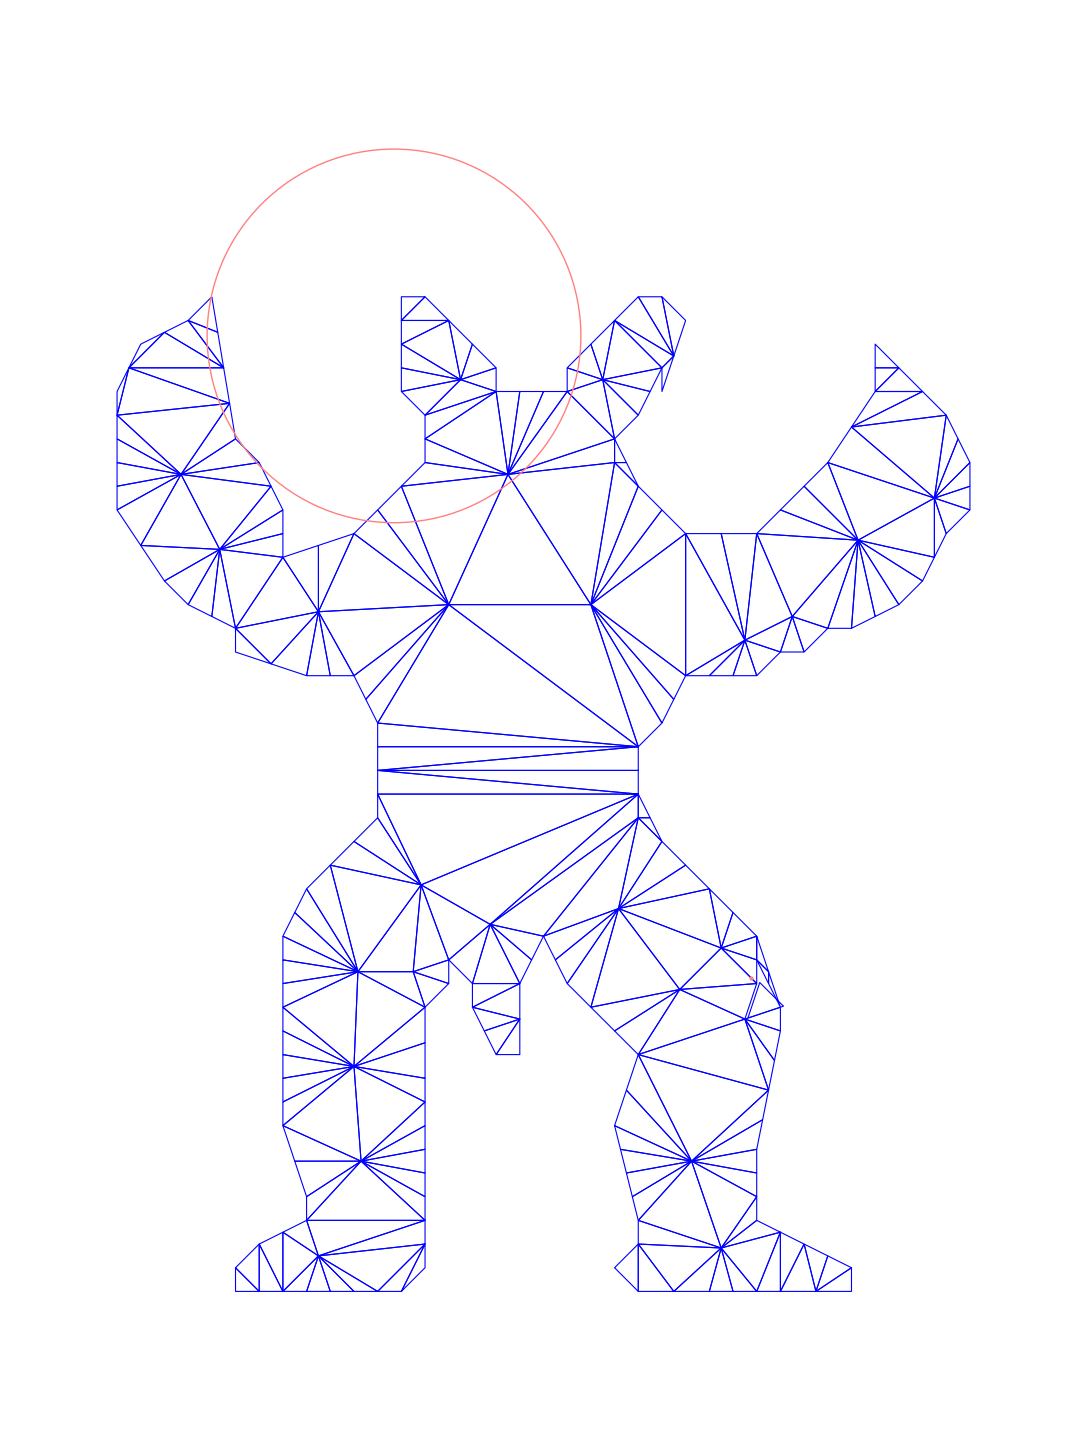

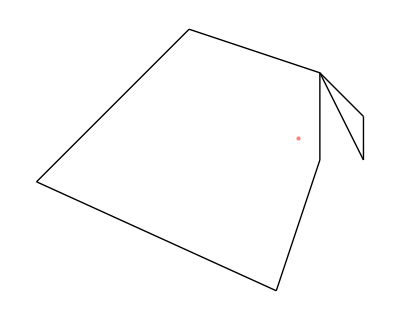

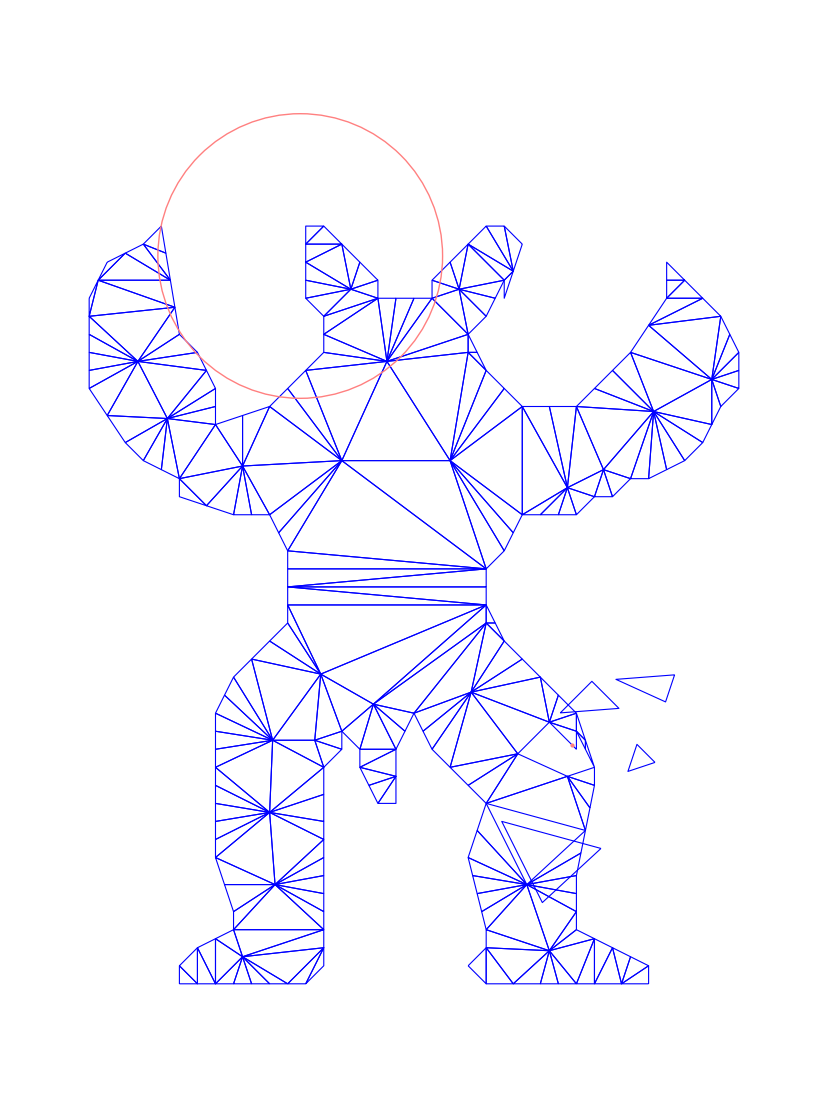

-Graphics-

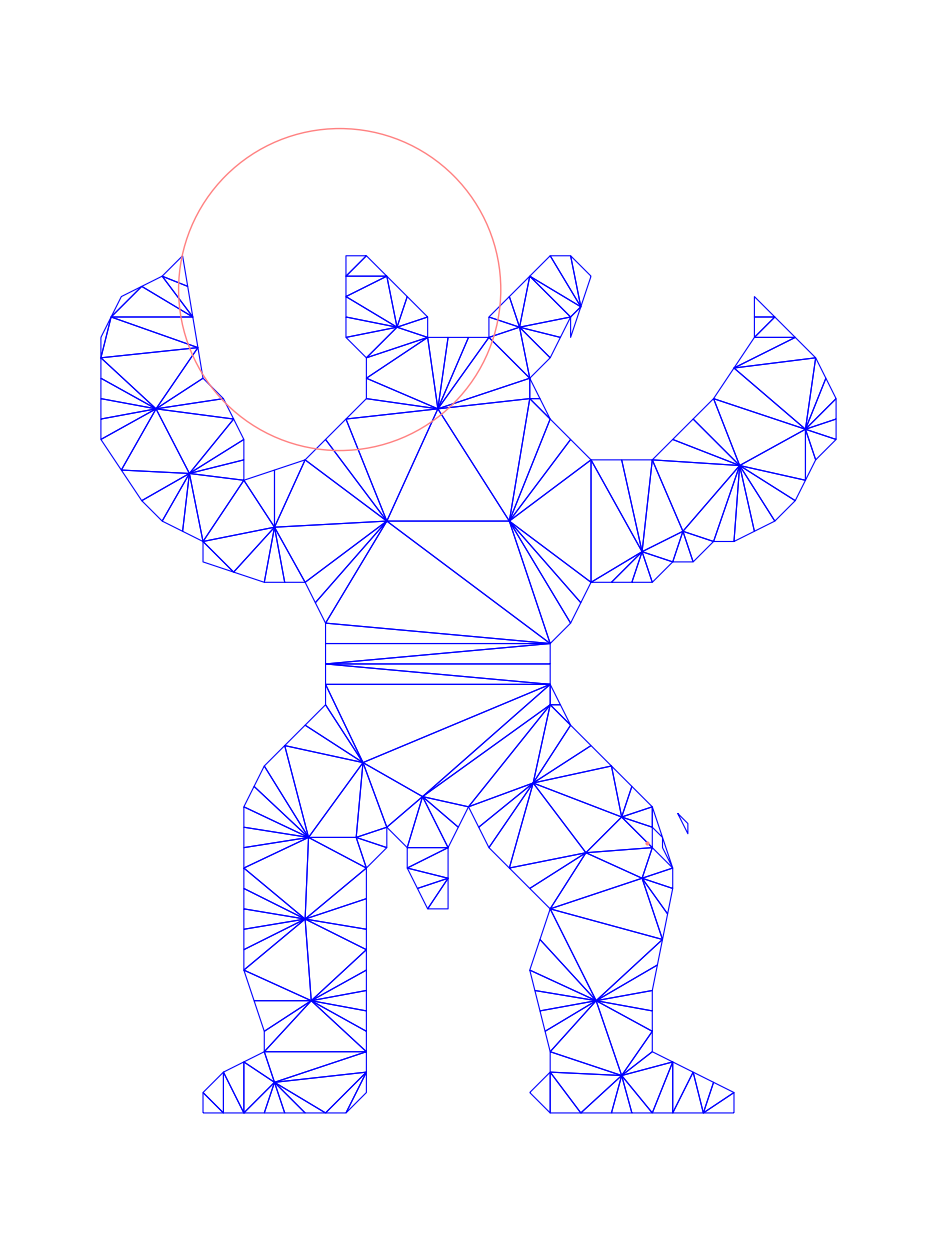

-Graphics-

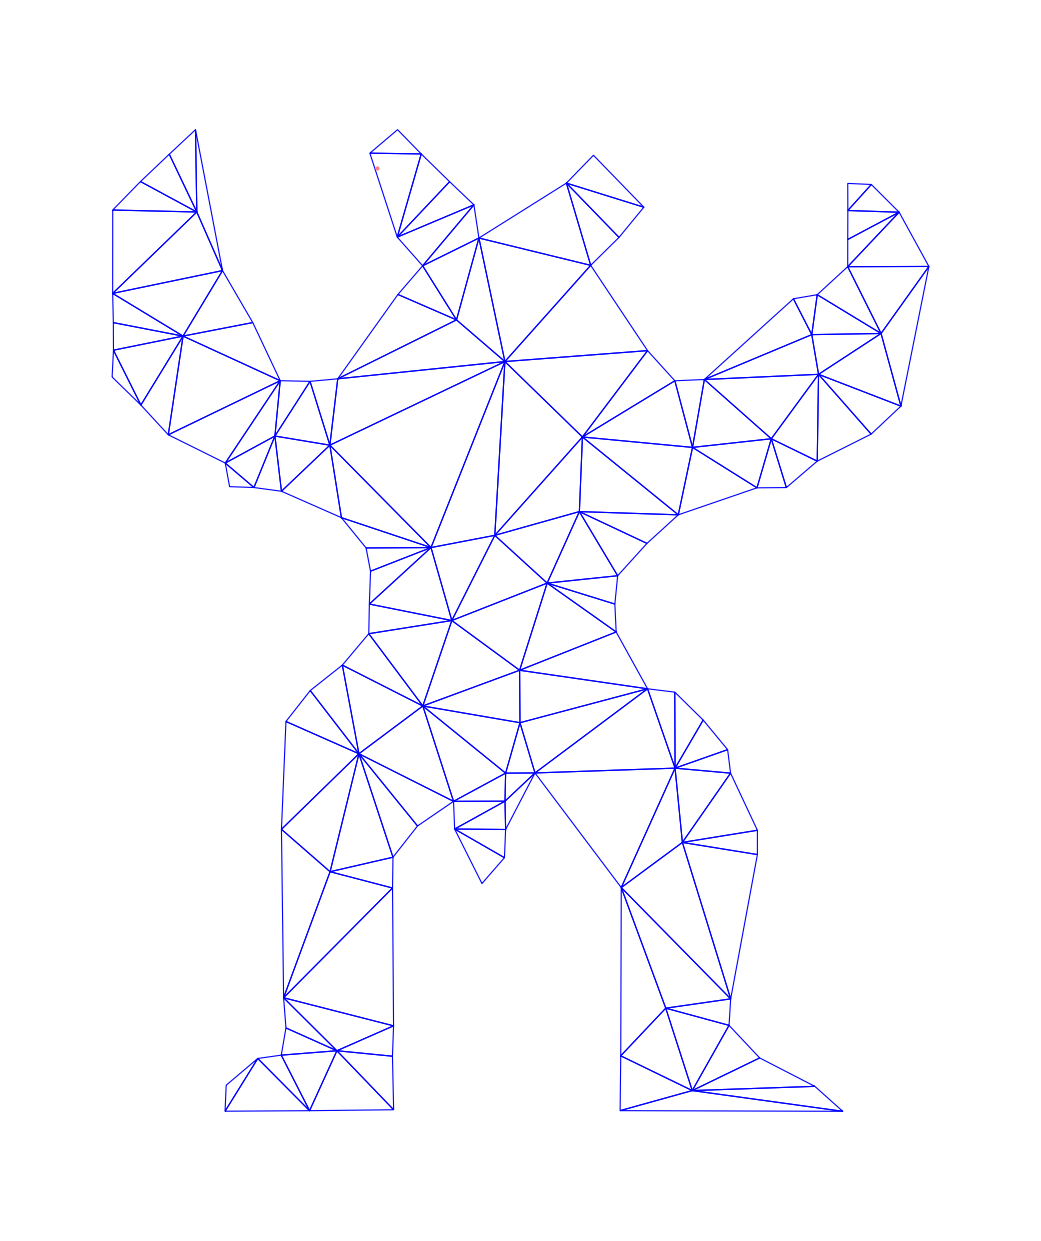

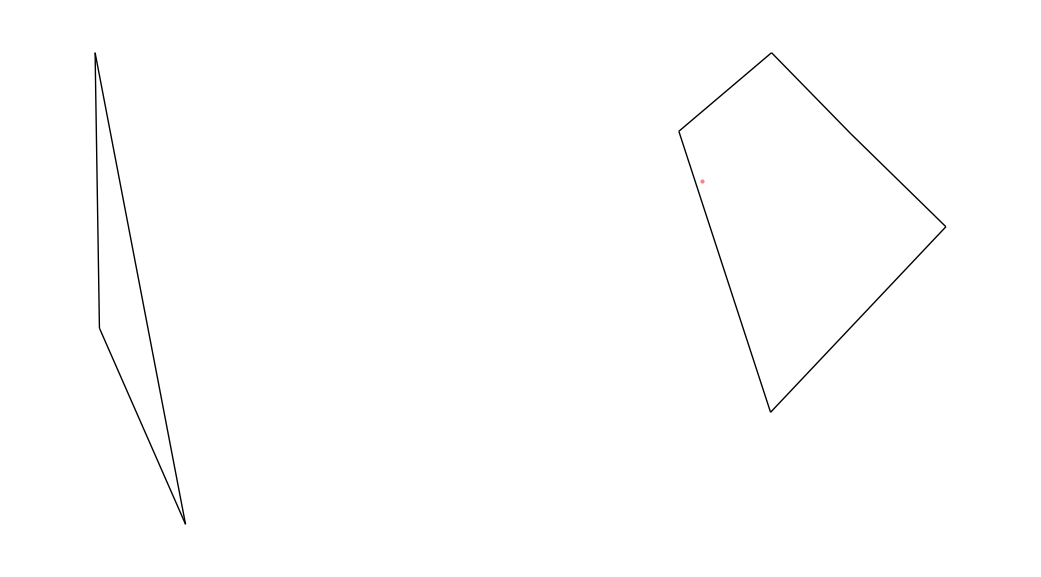

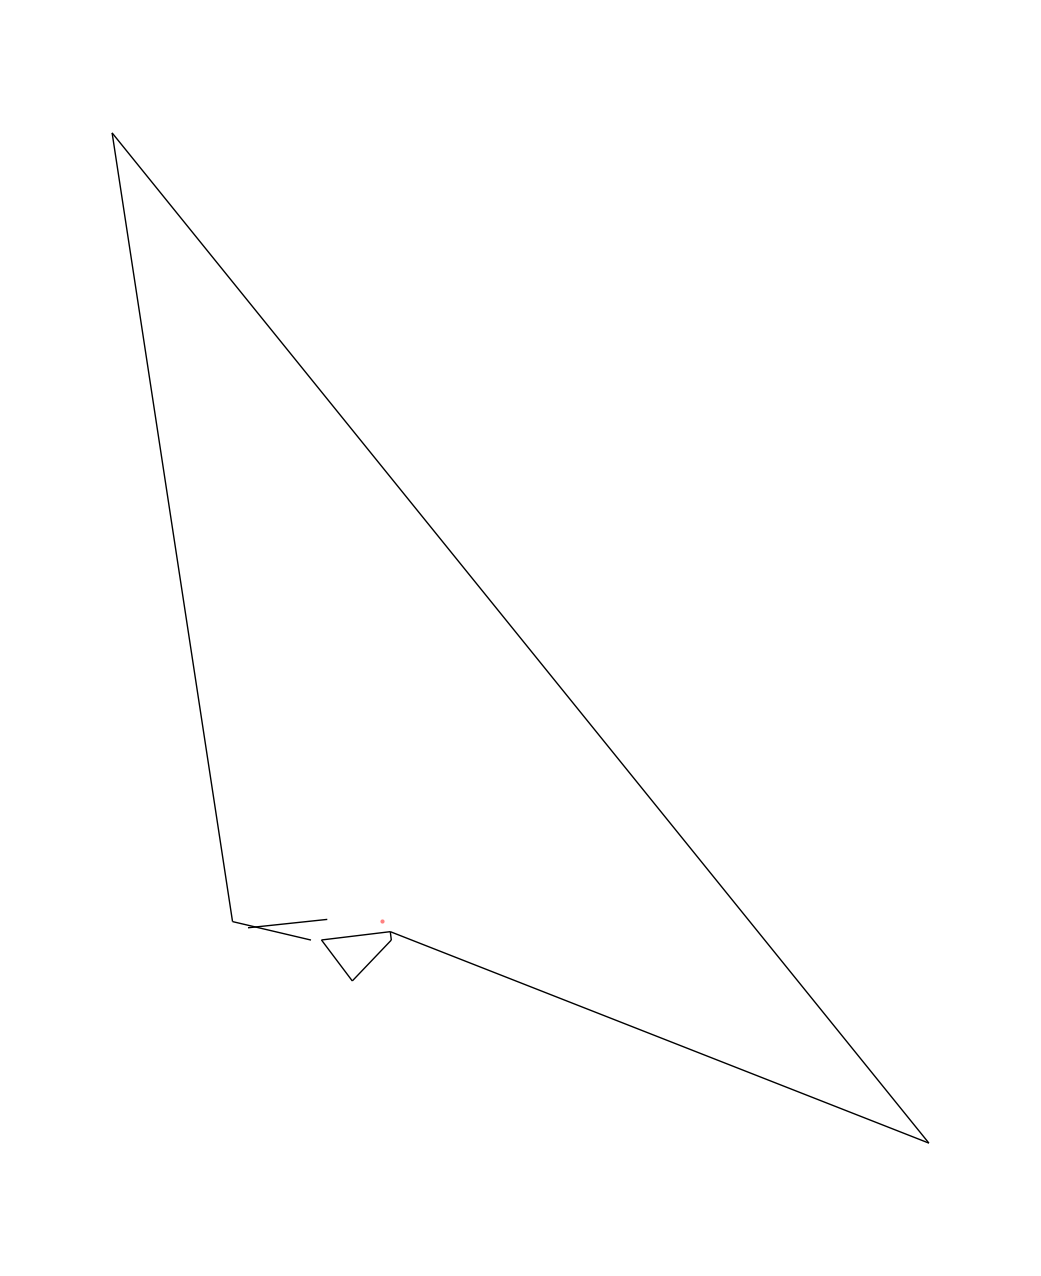

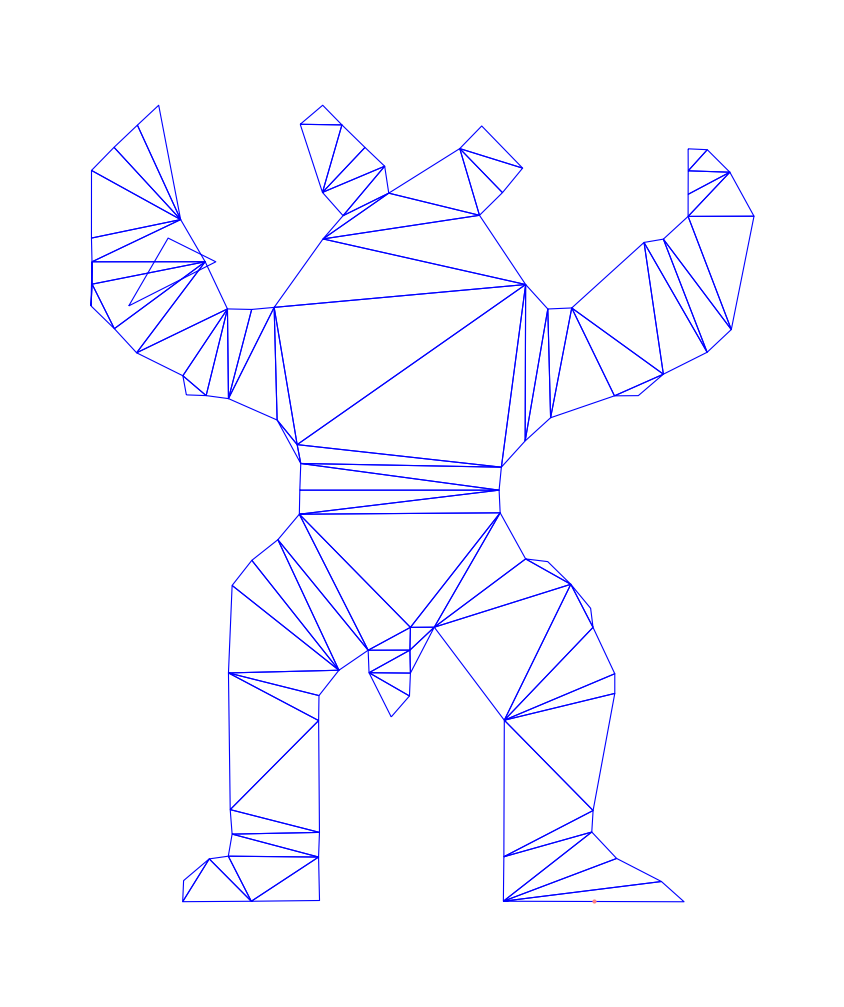

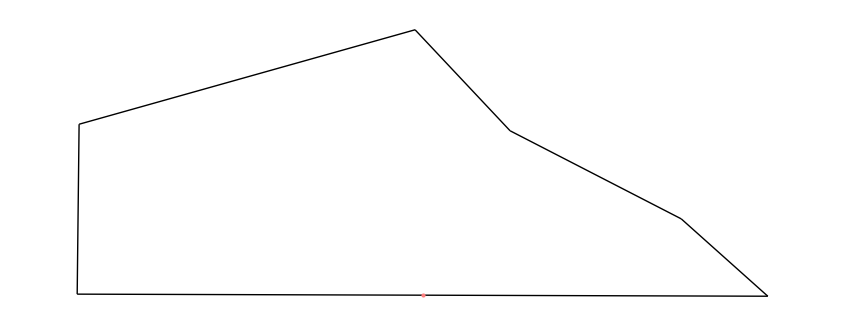

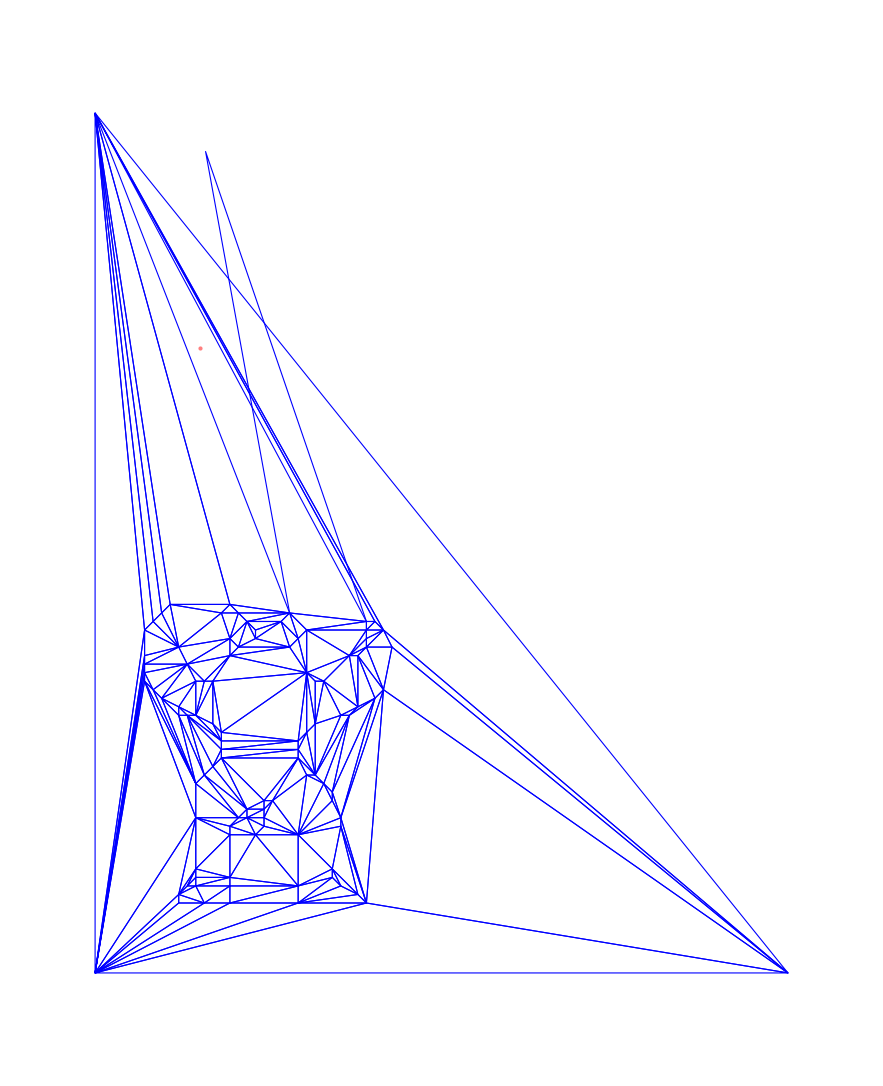

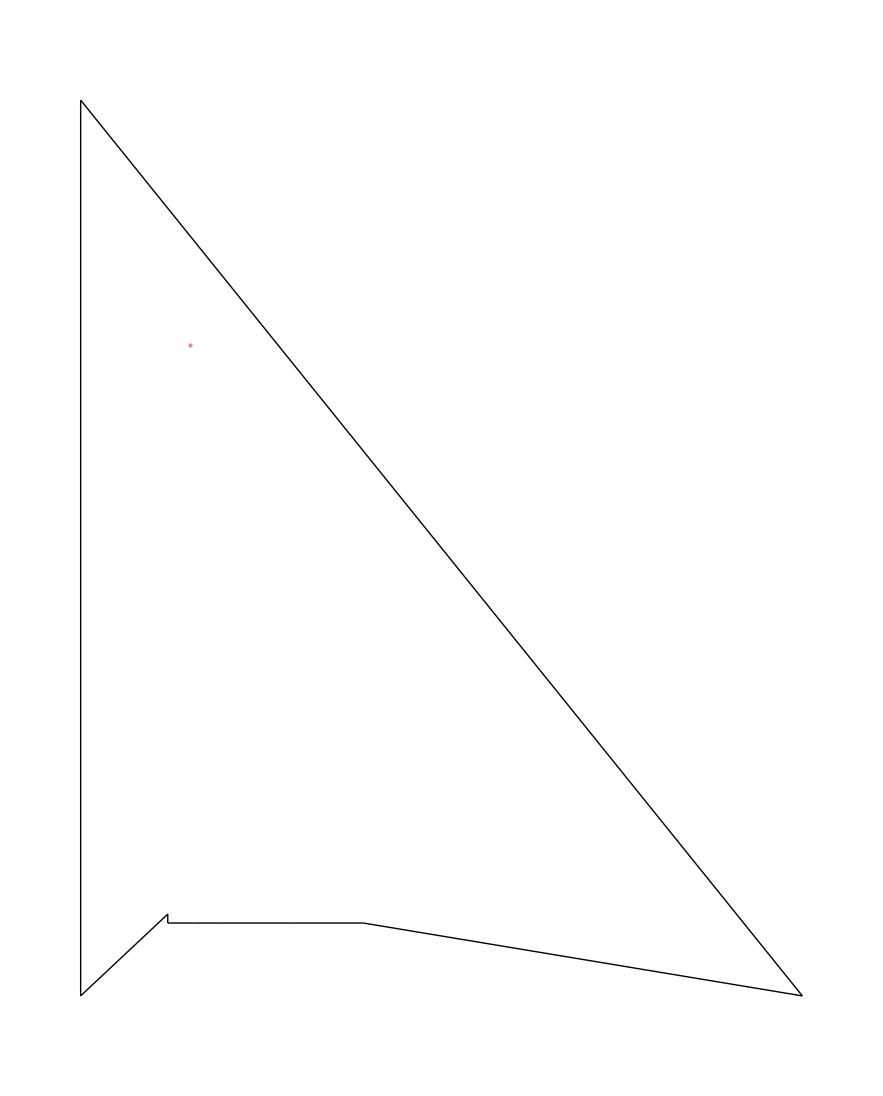

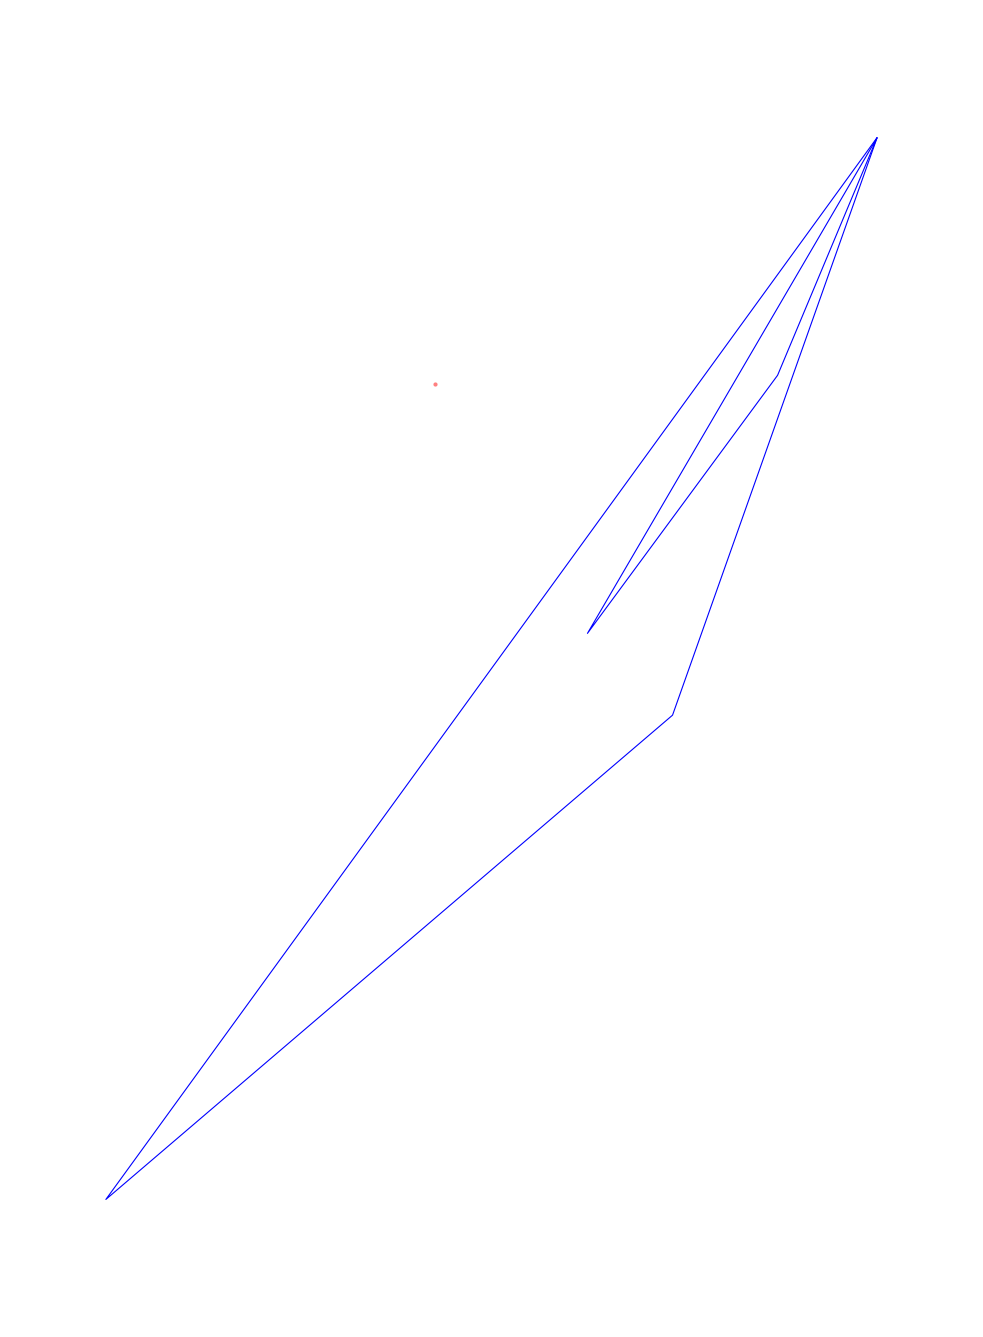

1

0.1

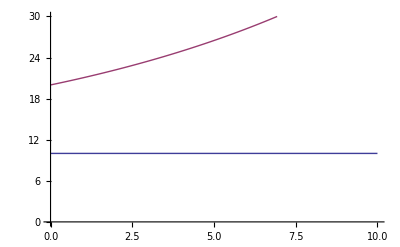

```mathematica
a = 1
k = 0.1

Plot[{a/k, (E^(k(t) ) + a) /k}, {t, 0, 10}, PlotRange->{0,30}]
```

{{0.111703,1.17912},{0.33559,1.49799},{-0.078785,1.49077}}

{0.129972,1.40433}

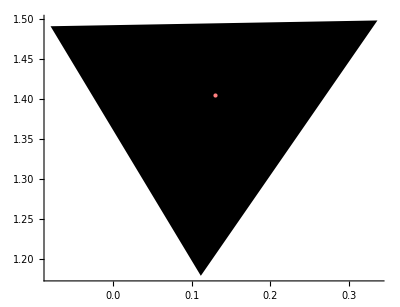

```mathematica
atri = {{0.111703,1.179124},{0.335590,1.497993},{-0.078785,1.490770}}
apt = {0.129972,1.404330}
Graphics[{Polygon[atri],Pink, Point[apt]}, Axes->True]
```